#### 1)

```mathematica
f=1/x^2-(x^2)^(1/3);
g=Log[x]/Tan[x];
h=Log[x^2/(x-1)];
D[f,x]
D[g,x]
D[h,x]//Simplify
```

-2/x^3-(2 x)/(3 (x^2)^(2/3))

Cot[x]/x-Csc[x]^2 Log[x]

(-2+x)/((-1+x) x)

#### 2)

```mathematica
f=x^(1/3);
Series[f,{x,1,2}]//Normal
%/.{x->0.9}
0.9^(1/3)
```

1+1/3 (-1+x)-1/9 (-1+x)^2

0.965556

0.965489

#### 3)

-60 x-30 x^2+4 x^3+3 x^4

-60-60 x+12 x^2+12 x^3

{{x→-1},{x→-√5},{x→√5}}

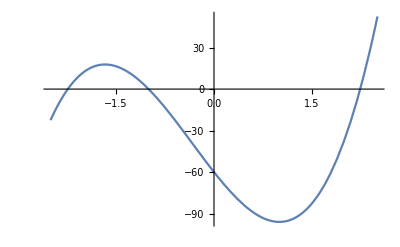

```mathematica
(x+1)(x^2-5)//Expand;
y1=Integrate[%,x]12//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-2.5,2.5}]
```

#### 4)

```mathematica
-1/(x+2)+2/(x-1)//Together;
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]//Expand
%%//TeXForm
```

(5+x)/(-2+x+x^2)

2 Log[1-x]-Log[2+x]

\frac{x+5}{x^2+x-2}

#### 5)

```mathematica
Integrate[2x-1/(√x),{x,1,4}]
Integrate[x^3/Sqrt[x^4+9],{x,0,2}]
```

13

1

#### 6)

3-4 x+x^2

{{x→1},{x→3}}

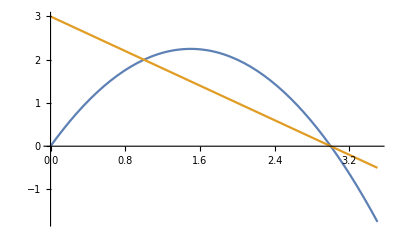

4/3

```mathematica
(x-1)(x-3)//Expand
y1=3x-x^2;
y2=3-x;
Solve[y1==y2,x]
Plot[{y1,y2},{x,0,3.5}]
Integrate[y1-y2,{x,1,3}]
```

#### 7)

3-2 x

-1

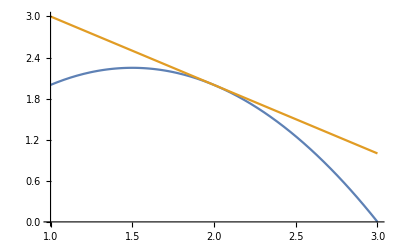

4-x

```mathematica
f1[x_]:=3x-x^2;
f1'[x]
x0=2;
f1'[x0]
g1[x_]:=f1'[x0](x-x0)+f1[x0];
Plot[{f1[x],g1[x]},{x,1,3}]
g1[x]
```

#### 8)

```mathematica
y1=-x;
y2=3x;
S=Integrate[(y2-y1),{x,0,1}]
Sy=Integrate[(y2-y1)x,{x,0,1}]
Sx=1/2Integrate[y2^2-y1^2,{x,0,1}]
```

2

4/3

4/3